```mathematica
seleccion1=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x},x]

seleccion2=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x,x^2},x]

seleccion3=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x,x^2,x^3},x]

seleccion4=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x,x^2,x^3,x^4},x]

seleccion8=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

puntos=ListPlot[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}}]
```

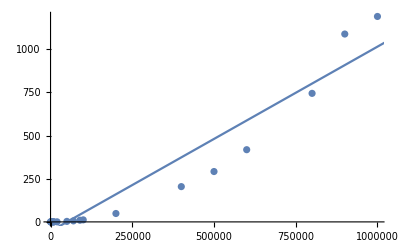

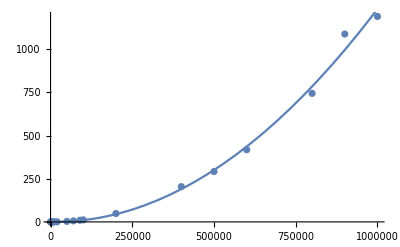

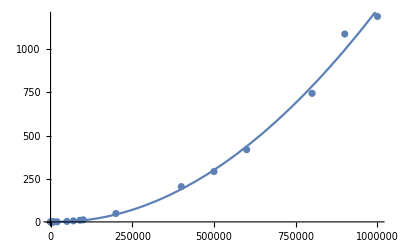

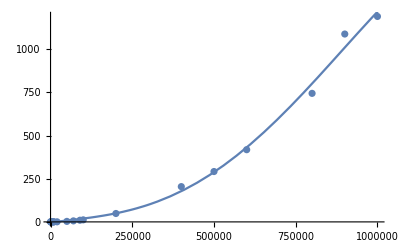

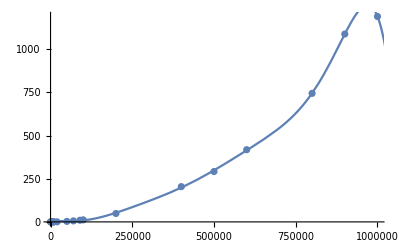

```mathematica
g1=Plot[seleccion1,{x,0,2000000}]
Show[puntos,g1]

g2=Plot[seleccion2,{x,0,2000000}]
Show[puntos,g2]

g3=Plot[seleccion3,{x,0,2000000}]
Show[puntos,g3]

g4=Plot[seleccion4,{x,0,2000000}]
Show[puntos,g4]

g8=Plot[seleccion8,{x,0,2000000}]
Show[puntos,g8]
```